# Prepare

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../neupackage/mma/neutrino.wl"]
```

```mathematica
Get["../../neupackage/mma/neumat.wl"]
```

```mathematica
colorpalette5={RGBColor[172,151,62],
RGBColor[129,118,204],
RGBColor[91,169,102],
RGBColor[199,90,147],
RGBColor[204,95,67]}
```

{RGBColor[172,151,62],RGBColor[129,118,204],RGBColor[91,169,102],RGBColor[199,90,147],RGBColor[204,95,67]}

```mathematica
markers=Graphics`PlotMarkers[]
```

{{●,8.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

## Rabi Oscillation

```mathematica
ampRabi[a_,k_,omegam_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2);
```

```mathematica
probRabi[a_,k_,omegam_,x_]:=Abs[a]^2/(Abs[a]^2+(k-omegam)^2)Sin[(√(Abs[a]^2+(k-omegam)^2))/2 x]^2;
```

## Parameters

Parameters

```mathematica
endpoint=140000;
endpoint2=400000;
endpoint3=100;
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
energy20=20;(*Energy in units of MeV*)
?OmegaVacuum
omegaV=OmegaVacuum[energy10,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093]/2
```

Takes [energy_,deltam2_] as parameters and calculates ω_v. Should becareful about units.

1.3×10^-16

0.154948

```mathematica
energy20=20;(*Energy in units of MeV*)
```

```mathematica
fraction=0.5(*0.99*)
lambdaN=fraction*Cos[2thetaV]omegaV (*MeV*)
```

0.5

6.19038×10^-17

```mathematica
thetamVN=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi];
```

```mathematica
omegaV=OmegaVacuum[energy20,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)
lambdaN=0.5*Cos[2thetaV]omegaV (*MeV*)
omegaM=OmegaMatter2[lambdaN,thetaV,omegaV](*MeV*)
thetamV=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi]
```

6.5×10^-17

3.09519×10^-17

3.67552×10^-17

0.198931

```mathematica
datafracStashFullTicks:=Table[{x,ScientificForm[MeVInverse2km[x/omegaM],2]},{x,0,endpoint}];
(*datafracStashTicks[i_]:=Take[datafracStashFullTicks[i],{1,Length@datafracStashFullTicks[i],Floor[(Length@datafracStashFullTicks[i])/5]}];*)
datafracStashTicks:=Table[{x,ScientificForm[MeVInverse2km[x/omegaM],2]},{x,0,endpoint,Floor[endpoint/5]}];
```

## Destruction Criteria

```mathematica
a2FromQ[a_,q_]:=√(2a q)
```

We can define the non-approximate formula for relative detuning

```mathematica
rDFull[omegam_,k1_,k2_,a1_,a2_]:=Abs[((omegam-k2)√(1+a2^2/(omegam-k2)^2)-(k1-k2))/a1]
```

```mathematica
rD[omegam_,k1_,k2_,a1_,a2_]:=Abs[((omegam-k1)+1/2 a2^2/(omegam-k2))/a1]
```

## Numerical Solutions

```mathematica
solNumRabi[kList_,aList_,endpointModule_]:=Module[{sysM,lenM},

lenM=Length@kList;

(*sysM=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(Total[Table[aList[[n]]Cos[kList[[n]]x],{n,1,lenM}]])PauliMatrix[1]/2(*+(Total[Table[aList[[n]]Sin[kList[[n]]x],{n,1,lenM}]])PauliMatrix[2]/2*)).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};
*)
sysM=I D[{psi1[x],psi2[x]},x]==(-PauliMatrix[3]/2-(Total[Table[aList[[n]]Cos[kList[[n]]x],{n,1,lenM}]])PauliMatrix[1]/2+(Total[Table[aList[[n]]Sin[kList[[n]]x],{n,1,lenM}]])PauliMatrix[2]/2(*+(Total[Table[aList[[n]]Sin[kList[[n]]x],{n,1,lenM}]])PauliMatrix[2]/2*)).{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

NDSolve[sysM,{psi1,psi2},{x,0,endpointModule}]
]
```

Linearize the solutions

```mathematica
solutionLists[solutions_,endpointModule_,stepsize_]:=Module[{lenM},
lenM=Length@solutions;

Table[
Table[{x,(Abs[psi2[x]]^2)/.solutions[[i,1]]},{x,0,endpointModule,stepsize}]
,{i,1,lenM}]
]

solutionNeutrinoLists[solutions_,endpointModule_,stepsize_]:=Module[{lenM},
lenM=Length@solutions;

Table[
Table[{x,(Abs[neumat`Private`psi2[x]]^2)/.solutions[[i,1]]},{x,0,endpointModule,stepsize}]
,{i,1,lenM}]
]
```

Calculate the gridlines

```mathematica
gridlinesFull[omegam_,kList_,aList_]:=1/(1+rDFull[omegam,kList[[1]],kList[[2]],aList[[1]],aList[[2]]]^2)
gridlines[omegam_,kList_,aList_]:=1/(1+rD[omegam,kList[[1]],kList[[2]],aList[[1]],aList[[2]]]^2)
qvaluesFull[omegam_,kList_,aList_]:=rDFull[omegam,kList[[1]],kList[[2]],aList[[1]],aList[[2]]]
qvalues[omegam_,kList_,aList_]:=rD[omegam,kList[[1]],kList[[2]],aList[[1]],aList[[2]]]
```

### A List of parameters

```mathematica
kList1={1,1/10};
aList1={0.0001,0.01};

(*For small k2*)

kList2={1,10};
aList2={0.0001,0.01};

(*For large k2>k1*)

kList3={1,1/10};
aList3={0.0001,0.05};

(*For small |k2| rotating in the other direction *)

kList4={1,10};
aList4={0.0001,0.05};

(*For large |k2|>k1 rotating in the other direction *)

kList5={1,-10};
aList5={0.0001,0.01};

(*For large |k2|>k1 rotating in the other direction *)

kList6={1,-1/10};
aList6={0.0001,0.01};

(*For small |k2| rotating in the other direction *)

kList7={1,-10};
aList7={0.0001,0.1};

(*For large |k2|>k1 rotating in the other direction, with larger amplitude *)

kList8={1,-1/10};
aList8={0.0001,0.1};

(*For small |k2| rotating in the other direction *)

kList9={1,-1/(10)};
aList9={0.0001,0.1};


kList10={1-10^(-4),1.5};
aList10={0.0001,0.01};

kList11={0.05,1+1/1.9};
aList11={0.001,1};
```

Construct the full list of k’s and a’s to test

```mathematica
(*kList={kList1,kList2,kList3,kList4,kList5,kList6,kList7,kList8,kList11};
aList={aList1,aList2,aList3,aList4,aList5,aList6,aList7,aList8,aList11};*)
kList={kList11};
aList={aList11};
```

```mathematica
ampRabi[1,1+1/1.9,1]
```

0.78308

### The solutions are

```mathematica
solNumRabiAll=Table[
solNumRabi[kList[[i]],aList[[i]],endpoint3],
{i,1,Length@kList}]
```

{{{psi1→InterpolatingFunction[…],psi2→InterpolatingFunction[…]}}}

The following is some test for each individual

```mathematica
(*solNumRabi0=solNumRabi[{kList1[[1]]},{aList1[[1]]},endpoint]*)
```

```mathematica
(*solNumRabi1=solNumRabi[kList1,aList1,endpoint]*)
```

```mathematica
(*solNumRabi2=solNumRabi[kList2,aList2,endpoint]*)
```

```mathematica
(*solNumRabi3=solNumRabi[kList3,aList3,endpoint]*)
```

```mathematica
(*solNumRabi4=solNumRabi[kList4,aList4,endpoint]*)
```

```mathematica
(*solNumRabi5=solNumRabi[kList5,aList5,endpoint]*)
```

```mathematica
(*solNumRabi6=solNumRabi[kList6,aList6,endpoint]*)
```

```mathematica
(*solNumRabi7=solNumRabi[kList7,aList7,endpoint]*)
```

```mathematica
(*solNumRabi10=solNumRabi[kList10,aList10,endpoint]*)
```

```mathematica
(*sol10List=solutionLists[{solNumRabi10},endpoint,100];*)
```

```mathematica
(*ListPlot[sol10List
,Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks}},PlotRange->{(*{0,2 10^5}*)Automatic,Automatic},PlotStyle->{Black,Red,Blue,Magenta,Cyan,Yellow,Green},PlotLegends->Placed["kList="<>ToString[N@kList10]<>"; aList="<>ToString[aList10]<>"; ω_m=0.5ω_MSW",{Center,Below}]]*)
```

### Visualization of the solutions

```mathematica
sols=solutionLists[solNumRabiAll,endpoint3,1];
```

```mathematica
gridlinesListFull=Table[gridlinesFull[1,kList[[i]],aList[[i]]],{i,1,Length@kList}]
gridlinesList=Table[gridlines[1,kList[[i]],aList[[i]]],{i,1,Length@kList}]
qvaluesFullList=Table[qvaluesFull[1,kList[[i]],aList[[i]]],{i,1,Length@kList}]
qvaluesList=Table[qvalues[1,kList[[i]],aList[[i]]],{i,1,Length@kList}]
```

{8.34011×10^-6}

{1.}

{346.268}

{3.33067×10^-13}

```mathematica
plotleg=Table["k="<>ToString[N@kList[[i]]]<>";a="<>ToString[N@aList[[i]]]<>";",{i,1,Length@kList}]
```

{k={0.05, 1.52632};a={0.001, 1.};}

List plot of the results

```mathematica
idxEnd=1;
ListPlot[
sols[[1;;idxEnd]]
,Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks}},GridLines->{None, gridlinesList[[1;;idxEnd]]},PlotRange->{(*{0,2 10^5}*){0,endpoint3},Automatic},PlotStyle->{Black,Red,Blue,Magenta,Cyan,Yellow,Green},PlotLegends->Placed[plotleg[[1;;idxEnd]],{Center,Below}]]
```

-Graphics-

### For Neutrinos

```mathematica
kListNeu1={1,1/10};
aListNeu1={0.0001,0.01}/(Sin[2thetamV]/2);

(*For small k2*)

kListNeu2={1,10};
aListNeu2={0.0001,0.01}/(Sin[2thetamV]/2);

(*For large k2>k1*)

kListNeu3={1,1/10};
aListNeu3={0.0001,0.05}/(Sin[2thetamV]/2);

(*For small |k2| rotating in the other direction *)

kListNeu4={1,10};
aListNeu4={0.0001,0.05}/(Sin[2thetamV]/2);
```

```mathematica
kListNeu={kListNeu1,kListNeu2,kListNeu3,kListNeu4};
aListNeu={aListNeu1,aListNeu2,aListNeu3,aListNeu4};
```

```mathematica
solNumNeutrinoAll=Table[solNum[kListNeu[[i]],aListNeu[[i]],{0,0},thetamV,endpoint],{i,1,Length@kListNeu}]
```

$Aborted

```mathematica
solsNeutrino=solutionNeutrinoLists[solNumNeutrinoAll,endpoint,100];
```

```mathematica
gridlinesListNeuFull=Table[gridlinesFull[1,kList[[i]],aList[[i]]],{i,1,Length@kList}]
gridlinesListNeu=Table[gridlines[1,kList[[i]],aList[[i]]],{i,1,Length@kList}]
qvaluesFullListNeu=Table[qvaluesFull[1,kList[[i]],aList[[i]]],{i,1,Length@kList}]
qvaluesListNeu=Table[qvalues[1,kList[[i]],aList[[i]]],{i,1,Length@kList}]
```

{0.764162,0.996923,0.00516518,0.341415,0.997938,0.828773,0.0461674,0.000485762}

{0.764151,0.996923,0.00515726,0.341412,0.997938,0.828767,0.0461656,0.000483766}

{0.555538,0.0555555,13.8782,1.38888,0.0454545,0.454536,4.54536,45.361}

{0.555556,0.0555556,13.8889,1.38889,0.0454545,0.454545,4.54545,45.4545}

```mathematica
plotlegNeu=Table["k="<>ToString[N@kListNeu[[i]]]<>";a="<>ToString[N@aListNeu[[i]]]<>";",{i,1,Length@kListNeu}]
```

{k={1., 0.1};a={0.000516197, 0.0516197};,k={1., 10.};a={0.000516197, 0.0516197};,k={1., 0.1};a={0.000516197, 0.258098};,k={1., 10.};a={0.000516197, 0.258098};}

```mathematica
solsNeutrinoPlt=ListPlot[
solsNeutrino[[1;;3]]
,Joined->True,ImageSize->imgsize,Frame->True,FrameLabel->{{"Transition Probability",None},{"x̂","Distance (km)"}},
FrameTicks->{{Automatic,Automatic},{Automatic,datafracStashTicks}},(*GridLines->{None, gridlinesList[[1;;4]]},*)PlotRange->{(*{0,2 10^5}*)Automatic,Automatic},PlotStyle->{Black,Red,Blue,Magenta,Cyan,Yellow,Green},PlotLegends->Placed[plotlegNeu[[1;;3]],{Center,Below}]]
```

-Graphics-

### Export Data

```mathematica
Table[
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-interference-a1-a2-"<>ToString[N@aList[[i,1]]]<>"-"<>ToString[N@aList[[i,2]]]<>"-k1-k2-"<>ToString[N@kList[[i,1]]]<>"-"<>ToString[N@kList[[i,2]]]<>".csv",sols[[i]]]
,{i,1,4}]
```

{../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-interference-a1-a2-0.0001-0.01-k1-k2-1.-0.1.csv,../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-interference-a1-a2-0.0001-0.01-k1-k2-1.-10..csv,../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-interference-a1-a2-0.0001-0.05-k1-k2-1.-0.1.csv,../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-interference-a1-a2-0.0001-0.05-k1-k2-1.-10..csv}

```mathematica
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-interference-theory-amplitude-"<>DateString["Year"]<>DateString["Month"]<>DateString["Day"]<>".csv",gridlinesList]
```

../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-interference-theory-amplitude-20170318.csv

```mathematica
DateString["ISODate"]
DateString["Year"]<>DateString["Month"]<>DateString["Day"]
```

ISODate

20170318

#### Export the neutrino oscillation data

```mathematica
Table[
Export["../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-2freq-interference-a1-a2-"<>ToString[N@aListNeu[[i,1]]]<>"-"<>ToString[N@aListNeu[[i,2]]]<>"-k1-k2-"<>ToString[N@kListNeu[[i,1]]]<>"-"<>ToString[N@kListNeu[[i,2]]]<>".csv",solsNeutrino[[i]]]
,{i,1,Length@kListNeu}]
```

{../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-2freq-interference-a1-a2-0.000516197-0.0516197-k1-k2-1.-0.1.csv,../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-2freq-interference-a1-a2-0.000516197-0.0516197-k1-k2-1.-10..csv,../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-2freq-interference-a1-a2-0.000516197-0.258098-k1-k2-1.-0.1.csv,../../ipynb/papers/assets/rabi-oscillations-energy-gap-change/paper-2freq-interference-a1-a2-0.000516197-0.258098-k1-k2-1.-10..csv}

```mathematica
(*Export["./paper-interference-plot.png",solsNeutrinoPlt]*)
```

```mathematica
Export["(*../../ipynb/papers/assets/rabi-oscillations-energy-gap-change*)/paper-interference-theory-amplitude-"<>DateString["ISODate"]<>".csv",gridlinesList]
```

Export::nodir: Directory "/Users/leima/github/neuphysics/codebase/mma/matter/ipynb/papers/assets/rabi-oscillations-energy-gap-change*)/" does not exist.

OpenWrite::noopen: Cannot open "/Users/leima/github/neuphysics/codebase/mma/matter/ipynb/papers/assets/rabi-oscillations-energy-gap-change*)/paper-interference-theory-amplitude-ISODate.csv".

$Failed

Calculate Relative Detunings

Using the neumat package

```mathematica
ClearAll@interGRID
```

```mathematica
interGRID[kListM_,aListM_,listRangeM_,interferenceQValueResonanceModeNListM_]:=Module[{interferenceQValueListPaperM,interferenceWidthListPaperM,interferenceGridListPaperM,displayRangeM},

(*listNGenerator[2,20]*)

(*displayRangeM=displayRangeMInput;*)
displayRangeM=1;;20;

interferenceQValueListPaperM=Part[qValueOrderdList[listRangeM,kListM,aListM,{0,0},thetamV],displayRangeM];

interferenceWidthListPaperM=Table[widthNList[interferenceQValueListPaperM[[i,1]],kListM,aListM,{0,0},thetamV],{i,1,Length@interferenceQValueListPaperM}];

interferenceGridListPaperM=Table[
{interferenceQValueListPaperM[[i,1]],interferenceQValueListPaperM[[i,2]],
interferenceWidthListPaperM[[i]],
interferenceWidthListPaperM[[i]]/(2 widthNList[interferenceQValueResonanceModeNListM,kListM,aListM,{0,0},thetamV]interferenceQValueListPaperM[[i,2]]),
2Pi/(interferenceWidthListPaperM[[i]]^2+(1-interferenceQValueListPaperM[[i,1]].kListM)^2)^(1/2)},
{i,1,Length@interferenceQValueListPaperM}];

Grid@PrependTo[
PrependTo[interferenceGridListPaperM,{"{n} List","RD","Width","RD Shifted 1st","Oscillation Wavelengthaa"}],
{ToString@N@kListM<>" & "<>ToString@N@aListM,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft}
]


]
```

```mathematica
interGRID[kList2,aList2,listNGenerator[2,20],{1,0}]
interGRID[kList1,aList1,listNGenerator[2,20],{1,0}]
interGRID[kList4,aList4,listNGenerator[2,20],{1,0}]
interGRID[kList3,aList3,listNGenerator[2,20],{1,0}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Set::write: Tag PrependTo in PrependTo[interferenceGridListPaperM$127497, {"{n} List", "RD", "Width", "RD Shifted 1st", "Oscillation Wavelengthaa"}] is Protected.

{1., 10.} & {0.0001, 0.01} |  |  |  | 
{n} List | RD | Width | RD Shifted 1st | Oscillation Wavelengthaa
{-19,2} | 0. | 1.49298×10^-107 | ComplexInfinity | 4.2085×10^107
{-9,1} | 0. | 5.01497×10^-49 | ComplexInfinity | 1.25289×10^49
{1,0} | 0. | 0.0000193724 | ComplexInfinity | 324336.
{11,-1} | 0. | 9.68668×10^-60 | ComplexInfinity | 6.48642×10^59
{0,1} | 4645.77 | 0.00193724 | 0.0107625 | 0.698132
{0,-1} | 5678.17 | 0.00193724 | 0.00880566 | 0.571199
{-1,0} | 103239. | 0.0000193724 | 4.84311×10^-6 | 3.14159
{0,2} | 2.12774×10^7 | 8.92964×10^-7 | 1.08318×10^-9 | 0.330694
{0,-2} | 2.35172×10^7 | 8.92964×10^-7 | 9.80019×10^-10 | 0.299199
{-1,1} | 9.95436×10^7 | 8.03668×10^-8 | 2.08377×10^-11 | 0.785398
{1,1} | 1.01806×10^8 | 9.82261×10^-8 | 2.49023×10^-11 | 0.628319
{-1,-1} | 1.22167×10^8 | 9.82261×10^-8 | 2.07519×10^-11 | 0.523599
{1,-1} | 1.24429×10^8 | 8.03668×10^-8 | 1.66701×10^-11 | 0.628319
{2,0} | 1.11987×10^9 | 8.92964×10^-10 | 2.05804×10^-14 | 6.28319
{-2,0} | 3.3596×10^9 | 8.92964×10^-10 | 6.86013×10^-15 | 2.0944
{0,3} | 1.40911×10^11 | 2.05804×10^-10 | 3.7696×10^-17 | 0.216662
{0,-3} | 1.50629×10^11 | 2.05804×10^-10 | 3.5264×10^-17 | 0.202683
{-1,2} | 4.60326×10^11 | 3.91028×10^-11 | 2.19244×10^-18 | 0.349066
{1,2} | 4.62761×10^11 | 4.32188×10^-11 | 2.41047×10^-18 | 0.314159
{-1,-2} | 5.09037×10^11 | 4.32188×10^-11 | 2.19134×10^-18 | 0.285599

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Set::write: Tag PrependTo in PrependTo[interferenceGridListPaperM$128704, {"{n} List", "RD", "Width", "RD Shifted 1st", "Oscillation Wavelengthaa"}] is Protected.

{1., 0.1} & {0.0001, 0.01} |  |  |  | 
{n} List | RD | Width | RD Shifted 1st | Oscillation Wavelengthaa
{-1,20} | 0. | 1.49282×10^-50 | ComplexInfinity | 4.20892×10^50
{0,10} | 0. | 5.014×10^-21 | ComplexInfinity | 1.25313×10^21
{1,0} | 0. | 0.0000193313 | ComplexInfinity | 325026.
{2,-10} | 0. | 5.32664×10^-30 | ComplexInfinity | 1.17958×10^30
{3,-20} | 0. | 5.28636×10^-60 | ComplexInfinity | 1.18857×10^60
{0,1} | 465.071 | 0.00193519 | 0.107625 | 6.9813
{0,-1} | 568.42 | 0.00193519 | 0.0880567 | 5.71198
{0,2} | 8965.27 | 0.0000892332 | 0.000257438 | 7.85398
{0,-2} | 13447.9 | 0.0000892332 | 0.000171625 | 5.23599
{1,1} | 101914. | 9.81218×10^-7 | 2.49023×10^-7 | 62.8319
{-1,0} | 103459. | 0.0000193313 | 4.83283×10^-6 | 3.14159
{1,-1} | 124562. | 8.02815×10^-7 | 1.66701×10^-7 | 62.8319
{0,3} | 340310. | 2.05695×10^-6 | 1.56335×10^-7 | 8.97598
{0,-3} | 632005. | 2.05695×10^-6 | 8.41805×10^-8 | 4.83322
{-1,-1} | 2.1402×10^6 | 9.81218×10^-7 | 1.18582×10^-8 | 2.99199
{-1,1} | 2.36667×10^6 | 8.02815×10^-7 | 8.77376×10^-9 | 3.30694
{1,2} | 8.10406×10^6 | 2.4679×10^-8 | 7.87651×10^-11 | 31.4159
{1,-2} | 1.21561×10^7 | 1.64527×10^-8 | 3.50067×10^-11 | 31.4159
{0,4} | 1.89825×10^7 | 3.1608×10^-8 | 4.30678×10^-11 | 10.472
{0,-4} | 4.42925×10^7 | 3.1608×10^-8 | 1.84576×10^-11 | 4.48799

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Set::write: Tag PrependTo in PrependTo[interferenceGridListPaperM$129911, {"{n} List", "RD", "Width", "RD Shifted 1st", "Oscillation Wavelengthaa"}] is Protected.

{1., 10.} & {0.0001, 0.05} |  |  |  | 
{n} List | RD | Width | RD Shifted 1st | Oscillation Wavelengthaa
{-19,2} | 0. | 3.73243×10^-106 | ComplexInfinity | 1.6834×10^106
{-9,1} | 0. | 2.50748×10^-48 | ComplexInfinity | 2.50578×10^48
{1,0} | 0. | 0.0000193723 | ComplexInfinity | 324338.
{11,-1} | 0. | 4.84333×10^-59 | ComplexInfinity | 1.29729×10^59
{0,1} | 929.157 | 0.0096862 | 0.269062 | 0.698131
{0,-1} | 1135.64 | 0.0096862 | 0.220141 | 0.571198
{-1,0} | 103240. | 0.0000193723 | 4.84309×10^-6 | 3.14159
{0,2} | 851099. | 0.0000223241 | 6.76988×10^-7 | 0.330694
{0,-2} | 940689. | 0.0000223241 | 6.12513×10^-7 | 0.299199
{-1,1} | 1.99088×10^7 | 4.01833×10^-7 | 5.20941×10^-10 | 0.785398
{1,1} | 2.03612×10^7 | 4.91129×10^-7 | 6.22557×10^-10 | 0.628319
{-1,-1} | 2.44335×10^7 | 4.91129×10^-7 | 5.18798×10^-10 | 0.523599
{1,-1} | 2.4886×10^7 | 4.01833×10^-7 | 4.16753×10^-10 | 0.628319
{2,0} | 1.11987×10^9 | 8.9296×10^-10 | 2.05803×10^-14 | 6.28319
{0,3} | 1.12729×10^9 | 2.57255×10^-8 | 5.89001×10^-13 | 0.216662
{0,-3} | 1.20503×10^9 | 2.57255×10^-8 | 5.51001×10^-13 | 0.202683
{-2,0} | 3.35961×10^9 | 8.9296×10^-10 | 6.8601×10^-15 | 2.0944
{-1,2} | 1.84131×10^10 | 9.77567×10^-10 | 1.37028×10^-15 | 0.349066
{1,2} | 1.85105×10^10 | 1.08047×10^-9 | 1.50655×10^-15 | 0.314159
{-1,-2} | 2.03615×10^10 | 1.08047×10^-9 | 1.36959×10^-15 | 0.285599

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Set::write: Tag PrependTo in PrependTo[interferenceGridListPaperM$131118, {"{n} List", "RD", "Width", "RD Shifted 1st", "Oscillation Wavelengthaa"}] is Protected.

{1., 0.1} & {0.0001, 0.05} |  |  |  | 
{n} List | RD | Width | RD Shifted 1st | Oscillation Wavelengthaa
{-1,20} | 0. | 1.42022×10^-36 | ComplexInfinity | 4.42411×10^36
{0,10} | 0. | 4.87383×10^-14 | ComplexInfinity | 1.28917×10^14
{1,0} | 0. | 0.000018357 | ComplexInfinity | 342277.
{2,-10} | 0. | 5.17774×10^-23 | ComplexInfinity | 1.2135×10^23
{3,-20} | 0. | 5.02924×10^-46 | ComplexInfinity | 1.24933×10^46
{0,1} | 95.4276 | 0.00943124 | 2.69192 | 6.98093
{0,-1} | 116.634 | 0.00943124 | 2.20248 | 5.71178
{0,2} | 364.773 | 0.00219315 | 0.163762 | 7.85395
{0,-2} | 547.159 | 0.00219315 | 0.109175 | 5.23598
{0,3} | 2757.46 | 0.000253857 | 0.00250754 | 8.97598
{0,-3} | 5120.99 | 0.000253857 | 0.00135021 | 4.83322
{1,1} | 20911.7 | 4.78202×10^-6 | 6.22859×10^-6 | 62.8319
{1,-1} | 25558.7 | 3.91256×10^-6 | 4.16955×10^-6 | 62.8319
{0,4} | 30683.6 | 0.0000195544 | 0.0000173582 | 10.472
{0,-4} | 71595.2 | 0.0000195544 | 7.43924×10^-6 | 4.48799
{-1,0} | 108950. | 0.000018357 | 4.58925×10^-6 | 3.14159
{1,2} | 329732. | 6.06553×10^-7 | 5.01043×10^-8 | 31.4159
{-1,-1} | 439145. | 4.78202×10^-6 | 2.966×10^-7 | 2.99199
{0,5} | 442991. | 1.12869×10^-6 | 6.93981×10^-8 | 12.5664
{-1,1} | 485616. | 3.91256×10^-6 | 2.1945×10^-7 | 3.30694

### Are these real

The question is:
for the first list of k’s and a’s
are the modes {0,1}, {0,-1} both important?
To check it, we compare the results by using NList {{1,0},{0,1}}, and {{1,0},{0,1},{0,,-1}}

```mathematica
hamilTest[x_]:=-PauliMatrix[3]/2+1/2{{0,widthNList[{1,0},kListNeu1,aListNeu1,{0,0},thetamV]Exp[-I kListNeu1[[1]]x]+widthNList[{0,1},kListNeu1,aListNeu1,{0,0},thetamV]Exp[-I kListNeu1[[2]]x]+widthNList[{0,-1},kListNeu1,aListNeu1,{0,0},thetamV]Exp[I kListNeu1[[2]]x]},{widthNList[{1,0},kListNeu1,aListNeu1,{0,0},thetamV]Exp[+I kListNeu1[[1]]x]+widthNList[{0,1},kListNeu1,aListNeu1,{0,0},thetamV]Exp[+I kListNeu1[[2]]x]+widthNList[{0,-1},kListNeu1,aListNeu1,{0,0},thetamV]Exp[-I kListNeu1[[2]]x],0}}
```

```mathematica
sysTest=I D[{psi1[x],psi2[x]},x]==hamilTest[x].{psi1[x],psi2[x]}&&{psi1[0],psi2[0]}=={1,0};

solTest=NDSolve[sysTest,{psi1,psi2},{x,0,endpoint}]
```

{{psi1→InterpolatingFunction[{{0., 140000.}}, <>],psi2→InterpolatingFunction[{{0., 140000.}}, <>]}}

```mathematica
?solNList
```

solution of a system composed of a given list of n's; Parameters taken are [listInput_,kNList_,aNList_,phiNList_,thetam_,endpoint_(*,workingprecision_:$MachinePrecision,accuracygoal_:0.5$MachinePrecision*)]

```mathematica
solTest2=solNList[{{1,0},{0,1},{0,-1},{0,2},{0,-2}},kListNeu1,aListNeu1,{0,0},thetamV,endpoint]
```

{{neumat`Private`psi1→InterpolatingFunction[{{0., 140000.}}, <>],neumat`Private`psi2→InterpolatingFunction[{{0., 140000.}}, <>]}}

```mathematica
solTestList=solutionNeutrinoLists[{solTest2},endpoint,100];
```

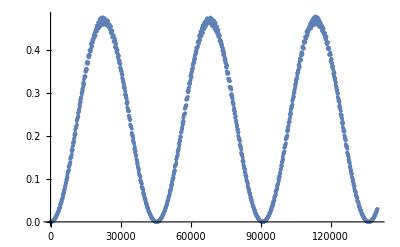

```mathematica
ListPlot[solTestList]
```

What to test

The function has been tested. Now for two frequencies, what should we test?

```mathematica
1/(1+2.6^2)
```

0.128866

```mathematica
Tan[2thetamV](kList4.{1,0}) BesselJ[1,aList4[[1]]/kList4[[1]]Cos[2thetamV]]BesselJ[0,aList4[[2]]/kList4[[2]]Cos[2thetamV]]
```

0.0000193723

```mathematica
BesselJ[1,aList4[[1]]/kList4[[1]]Cos[2thetamV]]
aList4[[1]]/kList4[[1]]Cos[2thetamV]
BesselJ[0,aList4[[2]]/kList4[[2]]Cos[2thetamV]]
aList4[[2]]/kList4[[2]]Cos[2thetamV]
```

0.0000460946

0.0000921891

0.999995

0.00460946

```mathematica
Tan[2thetamV](kList4.{1,0})
```

0.420276

```mathematica
Sin[2thetamV]
```

0.193725

```mathematica
Series[BesselJ[1,x],{x,0,1}]
```

x/2+O[x]^2